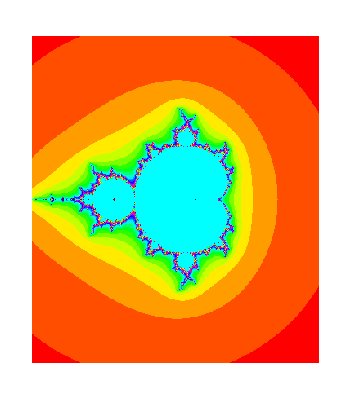

```mathematica
len[x0_,x_,d_]:=Which[Abs[x]>5.,d,Abs[x]<0.01,Infinity,True,If[d<100,1+len[x0,x^2+x0,d+1],0]]
a=Table[Table[len[i+I*j,i+I*j,0],{i,-2,1.5,0.01}],{j,-2,2,0.01}];
ArrayPlot[a,ColorFunction->Function[{x},Hue[x*5]]]
```

-0.825-0.2321 ⅈ

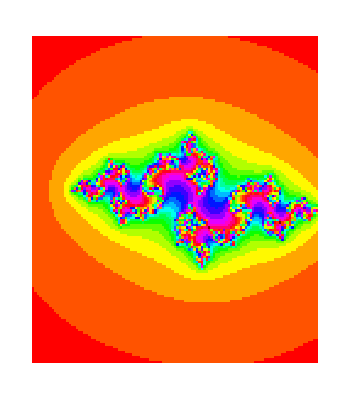

```mathematica
b=-0.825-0.2321I
len[x0_,x_,d_]:=Which[Abs[x]>5.,d,Abs[x]<0.01,Infinity,True,If[d<100,1+len[x0,x^2+b,d+1],0]]
a=Table[Table[len[i+I*j,i+I*j,0],{i,-2,1.5,0.03}],{j,-2,2,0.03}];
ArrayPlot[a,ColorFunction->Function[{x},Hue[x*5]]]
```

```mathematica
f[x0_,x_,d_]:=x^2+d
f[x0_,x_,9]:=0
NestList[f[x0_,#[[1]],#[[2]]]&,{RandomComplex[{-2-2I,2+2I}],0},10]
```

7.41421

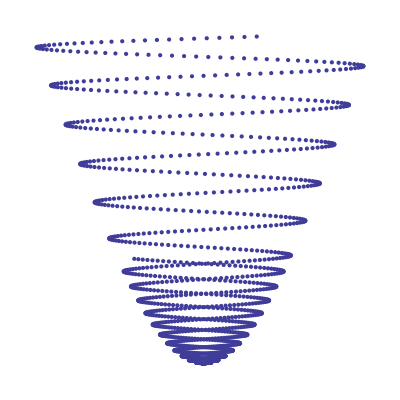

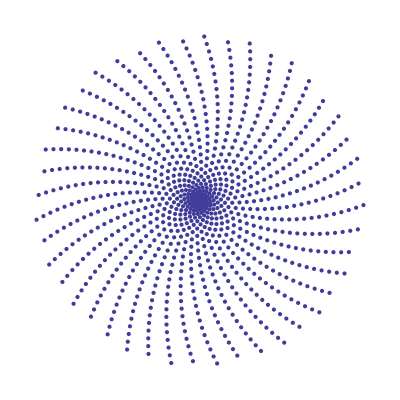

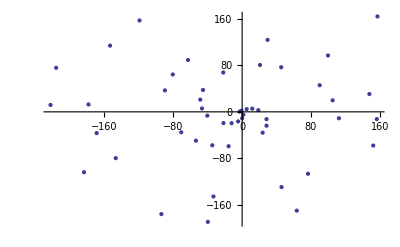

```mathematica
a=6+Sqrt[2]//N
({# a Cos[#*a],#Sin[#/a]}//N)&/@Identity/@Range[-5,10,0.01];
ListPlot[%,Axes->False,AspectRatio->1]
({#Cos[#],#Sin[#]}//N)&/@Identity/@Range[1000];
ListPlot[%,Axes->False,AspectRatio->1]
```

```mathematica
$MinPrecision=100;
Animate[ListPlot[({#*Cos[#/a],#  a Sin[ # a]}//N)&/@(Identity)/@Range[0,500,1],Axes->False,AspectRatio->1,PlotRange->{{-500,500},{500,-500}}],{a,1.31421,1.4,0.00007},AnimationRunning->False,AnimationRate->0.0005]
```

```mathematica
$MinPrecision=100;
q=2000.
Manipulate[ListPlot[({#*a*Cos[#*a],# a Sin[# a]}//N)&/@(Prime)/@Range[500],Axes->False,AspectRatio->1,PlotRange->{{-q,q},{q,-q}}],{a,2,3,0.00007}]
```

2000.

```mathematica
$MinPrecision=100;
q=2000.
Manipulate[ListPlot[({#*a*Cos[#*a],# a Sin[# a]}//N)&/@(Prime)/@Range[500],Axes->False,AspectRatio->1,PlotRange->{{-q,q},{q,-q}}],{a,2,3,0.00007}]
```

```mathematica
q=200;
Manipulate[ListPlot[({a #*Cos[a#],# a*Sin[#]}//N)&/@Identity/@Range[100],Axes->False,AspectRatio->1,PlotRange->{{-q,q},{q,-q}}],{a,2,3,0.00007}]
```

ListPlot::prng: Value of option PlotRange -> {{-q, q}, {q, -q}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

```mathematica
#&/@Range[10]//N
```

{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}

```mathematica
Manipulate[ArrayPlot[a,ColorFunction->Function[{x},Hue[x*5+i]]],{i,0,10,0.01}]
```

ArrayPlot::mat: Argument {4, 5, 5, 0, 9, 2, 8, 7, 0, 8, 4, 3, 6, 1, 7, 2, 9, 1, 7, 1, 6, 2, 0, 5, 6, 9, 5, 2, 3, 0, 2, 3, 1, 8, 3, 0, 9, 8, 5, 1, 4, 7, 3, 9, 8, 0, 9, 5, 7, 5, « 135 »} at position 1 is not a list of lists.

ArrayPlot::mat: Argument … at position 1 is not a list of lists.

```mathematica
b=-0.825-0.2321I
len[x0_,x_,d_,b_]:=Which[Abs[x]>5.,d,Abs[x]<0.01,Infinity,True,If[d<100,1+len[x0,x^2+b,d+1,b],0]]
```

-0.825-0.2321 ⅈ

```mathematica
Animate[ArrayPlot[Table[Table[len[i+I*j,i+I*j,0,b+0.5k+0.5*k*I],{i,-2,1.5,0.03}],{j,-2,2,0.03}],ColorFunction->Function[{x},Hue[x*5+(k)]]],{k,-1,2}, AnimationRunning->False, AnimationDirection->Forward,DisplayAllSteps->True]
Export["test.avi",%,"Duration"->120]
```

test.avi

```mathematica
a=Animate[Plot[Sin[x+k],{x,0,10}],{k,-1,2,0.001},  DefaultDuration->1200, Deployed->True,RefreshRate->24,DisplayAllSteps->True,AutorunSequencing->20];
Export["test.avi",a,"FrameRate"->24]
```

test.avi

```mathematica
RandomInteger[5,{5,5}]
```

{{3,5,2,1,2},{3,0,3,1,2},{3,5,5,3,2},{4,1,2,4,0},{0,5,3,3,1}}

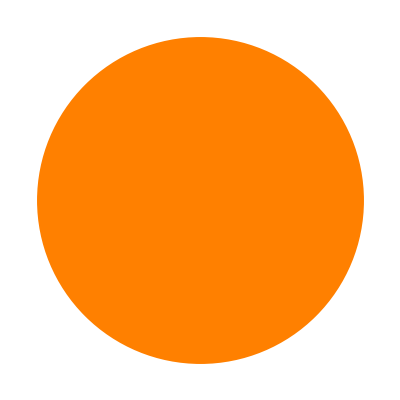

```mathematica
Graphics[{Hue,Disk[]}]
```

```mathematica
Range[0,3,0.5]
```

{0.,0.5,1.,1.5,2.,2.5,3.}

```mathematica
Export["test.avi",a,"FrameRate"->10]
```

test.avi